## grow-example.nb

Example Cellzilla2D notebook illustrating: 
	grow
	SimAnimate
	LineageAniamte
Portions of this notebook’s output have been suppressed (removed) to save space for internet display. All of the input cells included are sufficient to recover the output shown. 

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<xlr8r.m;
<<Cellzilla2D.m;
```

xCellerator 0.95 (28-Feb-2014) loaded Sat 20 Aug 2016 15:08:31
using Mathematica 8.0 for Microsoft Windows (64-bit) (October 6, 2011) (Version 8., Release 4)

Cellzilla2D (3.0.50 (21 Nov 2014)) loaded Sat 20 Aug 2016 15:08:32
using xCellerator 0.95 and XSSA 1.3.0
GPL License Terms Apply

### Generate A Template of 8 cells

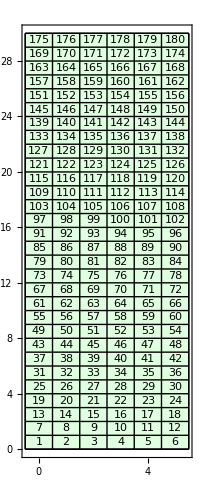

```mathematica
q=TemplateRectangular[{-1/2,5+1/2,1}, {0,30, 1}];
Q=Tissue2DTissue[q];
ShowTissue[Q,Frame-> True, "CellNumbers"-> True, "VertexNumbers"-> False]
```

### Define an internal pressure gradient in the template with the maximum in the second cell from the top and distributed via a bell curve

```mathematica
TC=Centroid[Q];
top=TissueVertices[Q][[18]];
f[i_]:=X[i]-> (BellCurve[1,top[[2]]-1.5,1.5][TC[[i,2]]]);
```

```mathematica
network={{∅->X,BellCurve[1, tip[2][t]-1.5,1.5][ycen[t]]}, {X-> ∅, 1}};
n=NTissueCells[Q];
centroids=Centroid[Q];
```

```mathematica
network
```

{{∅→X,1. ⅇ^(-0.222222 (1.5+ycen[t]-tip[2][t])^2)},{X→∅,1}}

```mathematica
myic=f/@Range[n]
```

{X[1]→1.,X[2]→1.,X[3]→1.,X[4]→1.,X[5]→1.,X[6]→1.,X[7]→0.800737,X[8]→0.800737,X[9]→0.800737,X[10]→0.800737,X[11]→0.800737,X[12]→0.800737,X[13]→0.411112,X[14]→0.411112,X[15]→0.411112,X[16]→0.411112,X[17]→0.411112,X[18]→0.411112,X[19]→0.135335,X[20]→0.135335,X[21]→0.135335,X[22]→0.135335,X[23]→0.135335,X[24]→0.135335,X[25]→0.0285655,X[26]→0.0285655,X[27]→0.0285655,X[28]→0.0285655,X[29]→0.0285655,X[30]→0.0285655,X[31]→0.00386592,X[32]→0.00386592,X[33]→0.00386592,X[34]→0.00386592,X[35]→0.00386592,X[36]→0.00386592,X[37]→0.000335463,X[38]→0.000335463,X[39]→0.000335463,X[40]→0.000335463,X[41]→0.000335463,X[42]→0.000335463,X[43]→0.0000186645,X[44]→0.0000186645,X[45]→0.0000186645,X[46]→0.0000186645,X[47]→0.0000186645,X[48]→0.0000186645,X[49]→6.65836×10^-7,X[50]→6.65836×10^-7,X[51]→6.65836×10^-7,X[52]→6.65836×10^-7,X[53]→6.65836×10^-7,X[54]→6.65836×10^-7,X[55]→1.523×10^-8,X[56]→1.523×10^-8,X[57]→1.523×10^-8,X[58]→1.523×10^-8,X[59]→1.523×10^-8,X[60]→1.523×10^-8,X[61]→2.23363×10^-10,X[62]→2.23363×10^-10,X[63]→2.23363×10^-10,X[64]→2.23363×10^-10,X[65]→2.23363×10^-10,X[66]→2.23363×10^-10,X[67]→2.10041×10^-12,X[68]→2.10041×10^-12,X[69]→2.10041×10^-12,X[70]→2.10041×10^-12,X[71]→2.10041×10^-12,X[72]→2.10041×10^-12,X[73]→1.26642×10^-14,X[74]→1.26642×10^-14,X[75]→1.26642×10^-14,X[76]→1.26642×10^-14,X[77]→1.26642×10^-14,X[78]→1.26642×10^-14,X[79]→4.89587×10^-17,X[80]→4.89587×10^-17,X[81]→4.89587×10^-17,X[82]→4.89587×10^-17,X[83]→4.89587×10^-17,X[84]→4.89587×10^-17,X[85]→1.21356×10^-19,X[86]→1.21356×10^-19,X[87]→1.21356×10^-19,X[88]→1.21356×10^-19,X[89]→1.21356×10^-19,X[90]→1.21356×10^-19,X[91]→1.92875×10^-22,X[92]→1.92875×10^-22,X[93]→1.92875×10^-22,X[94]→1.92875×10^-22,X[95]→1.92875×10^-22,X[96]→1.92875×10^-22,X[97]→1.96548×10^-25,X[98]→1.96548×10^-25,X[99]→1.96548×10^-25,X[100]→1.96548×10^-25,X[101]→1.96548×10^-25,X[102]→1.96548×10^-25,X[103]→1.28423×10^-28,X[104]→1.28423×10^-28,X[105]→1.28423×10^-28,X[106]→1.28423×10^-28,X[107]→1.28423×10^-28,X[108]→1.28423×10^-28,X[109]→5.38019×10^-32,X[110]→5.38019×10^-32,X[111]→5.38019×10^-32,X[112]→5.38019×10^-32,X[113]→5.38019×10^-32,X[114]→5.38019×10^-32,X[115]→1.44521×10^-35,X[116]→1.44521×10^-35,X[117]→1.44521×10^-35,X[118]→1.44521×10^-35,X[119]→1.44521×10^-35,X[120]→1.44521×10^-35,X[121]→2.48912×10^-39,X[122]→2.48912×10^-39,X[123]→2.48912×10^-39,X[124]→2.48912×10^-39,X[125]→2.48912×10^-39,X[126]→2.48912×10^-39,X[127]→2.74879×10^-43,X[128]→2.74879×10^-43,X[129]→2.74879×10^-43,X[130]→2.74879×10^-43,X[131]→2.74879×10^-43,X[132]→2.74879×10^-43,X[133]→1.94633×10^-47,X[134]→1.94633×10^-47,X[135]→1.94633×10^-47,X[136]→1.94633×10^-47,X[137]→1.94633×10^-47,X[138]→1.94633×10^-47,X[139]→8.83631×10^-52,X[140]→8.83631×10^-52,X[141]→8.83631×10^-52,X[142]→8.83631×10^-52,X[143]→8.83631×10^-52,X[144]→8.83631×10^-52,X[145]→2.57221×10^-56,X[146]→2.57221×10^-56,X[147]→2.57221×10^-56,X[148]→2.57221×10^-56,X[149]→2.57221×10^-56,X[150]→2.57221×10^-56,X[151]→4.80089×10^-61,X[152]→4.80089×10^-61,X[153]→4.80089×10^-61,X[154]→4.80089×10^-61,X[155]→4.80089×10^-61,X[156]→4.80089×10^-61,X[157]→5.74537×10^-66,X[158]→5.74537×10^-66,X[159]→5.74537×10^-66,X[160]→5.74537×10^-66,X[161]→5.74537×10^-66,X[162]→5.74537×10^-66,X[163]→4.40853×10^-71,X[164]→4.40853×10^-71,X[165]→4.40853×10^-71,X[166]→4.40853×10^-71,X[167]→4.40853×10^-71,X[168]→4.40853×10^-71,X[169]→2.16895×10^-76,X[170]→2.16895×10^-76,X[171]→2.16895×10^-76,X[172]→2.16895×10^-76,X[173]→2.16895×10^-76,X[174]→2.16895×10^-76,X[175]→6.84206×10^-82,X[176]→6.84206×10^-82,X[177]→6.84206×10^-82,X[178]→6.84206×10^-82,X[179]→6.84206×10^-82,X[180]→6.84206×10^-82}

### run the simulation for 100,000 time units

```mathematica
SIM=grow[Q,0,100000,
"center"-> cen,
"L1Anticlinal"-> False,
"Intercellular"-> {}, 
"IC"-> myic, 
"Walls"-> False, 
"mumax"-> 1, "mumin"-> 1,"muMaxDegrees"-> 90.0,
"IsotropicGrowth"-> False, 
"kmin"-> 1, "kmax"->1, "kMaxDegrees"-> 0, 
"IsotropicSprings"-> False, 
"TestCase"-> "Grow-Example", 
"IgnoreDivisionRadius"-> Infinity, 
"MaxRadius"-> Infinity, 
"Reactions"-> network, 
"Pumps"-> {},
"Diffusion"-> {}, 
"WallReactions"->{},
"BoundaryConditions"-> {X-> 0}, 
"EdgeVariable"-> ell,
"CellVariable"-> area,
"Growing"-> True,
"Restlength"-> resting,
"k"-> {k, 1&}, 
"mu"-> {μ, .01(.1 + 10*(X[#1][t]+X[#2][t]))&},
"P"-> {P, .01*(.05+100*X[#][t])&}, 
"DivisionModel"-> "Errera",
"Parameters"-> {}, 
"DivisionThreshold"-> 1.1, 
"DivisionSigma"-> 0.10, 
"DivisionVariable"-> area, 
"MinAngleSpread"->135,
"Verbose"-> False, 
"Origin"-> {0, 0}, 
"ShowOptions"-> {Frame-> True,ImageSize-> 512, "CellNumbers"-> False, "EdgeNumbers"-> False, 
PlotRange-> {{-12.5,12.5}, {-5,25}}}
];
```

simdir = C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0001.png

Actual Clock Time:  | 21-Aug-2016-at-02:20:06
Memory in Use (GB):  | 0.122133
Max Memory Used (GB):  | 0.146454
Free Memory (GB):  | 3.26914

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«14 more identical outputs»

Cell 7 (static cell 7) divides at t = 0.00160281

Cell 12 (static cell 12) divides at t = 0.00160281

Cell 19 (static cell 19) divides at t = 0.00160281

Cell 25 (static cell 25) divides at t = 0.00160281

Cell 30 (static cell 30) divides at t = 0.00160281

Cell 31 (static cell 31) divides at t = 0.00160281

Cell 84 (static cell 84) divides at t = 0.00160281

Cell 102 (static cell 102) divides at t = 0.00160281

Cell 103 (static cell 103) divides at t = 0.00160281

Cell 108 (static cell 108) divides at t = 0.00160281

Cell 127 (static cell 127) divides at t = 0.00160281

Cell 132 (static cell 132) divides at t = 0.00160281

Cell 133 (static cell 133) divides at t = 0.00160281

Cell 139 (static cell 139) divides at t = 0.00160281

Cell 145 (static cell 145) divides at t = 0.00160281

Cell 174 (static cell 174) divides at t = 0.00160281

Cell 180 (static cell 180) divides at t = 0.00160281

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0002.png

Actual Clock Time:  | 21-Aug-2016-at-02:21:44
Memory in Use (GB):  | 0.146843
Max Memory Used (GB):  | 0.270651
Free Memory (GB):  | 3.10065
CPU Used(seconds):  | 98.873
Number of Cells:  | 197
Cell Divisions:  | 17
Simulator Steps:  | 2
Number of Variables:  | 3893

Cell Division Errera's Method

Cell Division Errera's Method

Cell 3 (static cell 3) divides at t = 0.0171411

Cell 175 (static cell 175) divides at t = 0.0171411

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0003.png

Actual Clock Time:  | 21-Aug-2016-at-02:23:33
Memory in Use (GB):  | 0.171235
Max Memory Used (GB):  | 0.300685
Free Memory (GB):  | 2.70052
CPU Used(seconds):  | 206.701
Number of Cells:  | 199
Cell Divisions:  | 19
Simulator Steps:  | 3
Number of Variables:  | 4369

Cell Division Errera's Method

Cell 6 (static cell 6) divides at t = 0.0250876

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0004.png

Actual Clock Time:  | 21-Aug-2016-at-02:25:14
Memory in Use (GB):  | 0.186176
Max Memory Used (GB):  | 0.325241
Free Memory (GB):  | 2.54474
CPU Used(seconds):  | 306.074
Number of Cells:  | 200
Cell Divisions:  | 20
Simulator Steps:  | 4
Number of Variables:  | 4425

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 13 (static cell 13) divides at t = 0.0458502

Cell 72 (static cell 72) divides at t = 0.0458502

Cell 138 (static cell 138) divides at t = 0.0458502

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0005.png

Actual Clock Time:  | 21-Aug-2016-at-02:27:13
Memory in Use (GB):  | 0.208562
Max Memory Used (GB):  | 0.340268
Free Memory (GB):  | 2.40029
CPU Used(seconds):  | 424.525
Number of Cells:  | 203
Cell Divisions:  | 23
Simulator Steps:  | 5
Number of Variables:  | 4453

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«8 more identical outputs»

Cell 41 (static cell 41) divides at t = 0.0522653

Cell 43 (static cell 43) divides at t = 0.0522653

Cell 56 (static cell 56) divides at t = 0.0522653

Cell 71 (static cell 71) divides at t = 0.0522653

Cell 79 (static cell 79) divides at t = 0.0522653

Cell 115 (static cell 115) divides at t = 0.0522653

Cell 119 (static cell 119) divides at t = 0.0522653

Cell 155 (static cell 155) divides at t = 0.0522653

Cell 158 (static cell 158) divides at t = 0.0522653

Cell 161 (static cell 161) divides at t = 0.0522653

Cell 172 (static cell 172) divides at t = 0.0522653

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0006.png

Actual Clock Time:  | 21-Aug-2016-at-02:29:16
Memory in Use (GB):  | 0.230835
Max Memory Used (GB):  | 0.370138
Free Memory (GB):  | 2.4841
CPU Used(seconds):  | 546.549
Number of Cells:  | 214
Cell Divisions:  | 34
Simulator Steps:  | 6
Number of Variables:  | 4537

Cell Division Errera's Method

Cell Division Errera's Method

Cell 11 (static cell 11) divides at t = 0.0910227

Cell 55 (static cell 55) divides at t = 0.0910227

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0007.png

Actual Clock Time:  | 21-Aug-2016-at-02:31:20
Memory in Use (GB):  | 0.251644
Max Memory Used (GB):  | 0.400391
Free Memory (GB):  | 2.41879
CPU Used(seconds):  | 669.712
Number of Cells:  | 216
Cell Divisions:  | 36
Simulator Steps:  | 7
Number of Variables:  | 4845

Cell Division Errera's Method

Cell Division Errera's Method

Cell 144 (static cell 144) divides at t = 0.107785

Cell 178 (static cell 178) divides at t = 0.107785

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0008.png

Actual Clock Time:  | 21-Aug-2016-at-02:33:30
Memory in Use (GB):  | 0.270111
Max Memory Used (GB):  | 0.422222
Free Memory (GB):  | 2.4977
CPU Used(seconds):  | 798.319
Number of Cells:  | 218
Cell Divisions:  | 38
Simulator Steps:  | 8
Number of Variables:  | 4901

Cell Division Errera's Method

Cell Division Errera's Method

Cell 5 (static cell 5) divides at t = 0.118753

Cell 162 (static cell 162) divides at t = 0.118753

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0009.png

Actual Clock Time:  | 21-Aug-2016-at-02:35:39
Memory in Use (GB):  | 0.291483
Max Memory Used (GB):  | 0.442765
Free Memory (GB):  | 2.41775
CPU Used(seconds):  | 926.864
Number of Cells:  | 220
Cell Divisions:  | 40
Simulator Steps:  | 9
Number of Variables:  | 4957

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«2 more identical outputs»

Cell 42 (static cell 42) divides at t = 0.127784

Cell 61 (static cell 61) divides at t = 0.127784

Cell 67 (static cell 67) divides at t = 0.127784

Cell 109 (static cell 109) divides at t = 0.127784

Cell 179 (static cell 179) divides at t = 0.127784

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0010.png

Actual Clock Time:  | 21-Aug-2016-at-02:38:14
Memory in Use (GB):  | 0.315939
Max Memory Used (GB):  | 0.4653
Free Memory (GB):  | 2.30429
CPU Used(seconds):  | 1080.95
Number of Cells:  | 225
Cell Divisions:  | 45
Simulator Steps:  | 10
Number of Variables:  | 5013

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 24 (static cell 24) divides at t = 0.151258

Cell 91 (static cell 91) divides at t = 0.151258

Cell 157 (static cell 157) divides at t = 0.151258

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0011.png

Actual Clock Time:  | 21-Aug-2016-at-02:40:53
Memory in Use (GB):  | 0.335759
Max Memory Used (GB):  | 0.495143
Free Memory (GB):  | 2.2416
CPU Used(seconds):  | 1238.77
Number of Cells:  | 228
Cell Divisions:  | 48
Simulator Steps:  | 11
Number of Variables:  | 5153

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«2 more identical outputs»

Cell 1 (static cell 1) divides at t = 0.164096

Cell 62 (static cell 62) divides at t = 0.164096

Cell 97 (static cell 97) divides at t = 0.164096

Cell 114 (static cell 114) divides at t = 0.164096

Cell 151 (static cell 151) divides at t = 0.164096

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0012.png

Actual Clock Time:  | 21-Aug-2016-at-02:43:47
Memory in Use (GB):  | 0.365597
Max Memory Used (GB):  | 0.532467
Free Memory (GB):  | 2.32924
CPU Used(seconds):  | 1411.19
Number of Cells:  | 233
Cell Divisions:  | 53
Simulator Steps:  | 12
Number of Variables:  | 5237

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«1 more identical outputs»

Cell 2 (static cell 2) divides at t = 0.192025

Cell 4 (static cell 4) divides at t = 0.192025

Cell 60 (static cell 60) divides at t = 0.192025

Cell 96 (static cell 96) divides at t = 0.192025

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0013.png

Actual Clock Time:  | 21-Aug-2016-at-02:46:35
Memory in Use (GB):  | 0.387606
Max Memory Used (GB):  | 0.553067
Free Memory (GB):  | 2.3905
CPU Used(seconds):  | 1578.71
Number of Cells:  | 237
Cell Divisions:  | 57
Simulator Steps:  | 13
Number of Variables:  | 5377

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«2 more identical outputs»

Cell 52 (static cell 52) divides at t = 0.211051

Cell 58 (static cell 58) divides at t = 0.211051

Cell 85 (static cell 85) divides at t = 0.211051

Cell 120 (static cell 120) divides at t = 0.211051

Cell 176 (static cell 176) divides at t = 0.211051

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0014.png

Actual Clock Time:  | 21-Aug-2016-at-02:49:40
Memory in Use (GB):  | 0.409427
Max Memory Used (GB):  | 0.578907
Free Memory (GB):  | 2.30144
CPU Used(seconds):  | 1762.58
Number of Cells:  | 242
Cell Divisions:  | 62
Simulator Steps:  | 14
Number of Variables:  | 5489

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«2 more identical outputs»

Cell 14 (static cell 14) divides at t = 0.227929

Cell 18 (static cell 18) divides at t = 0.227929

Cell 93 (static cell 93) divides at t = 0.227929

Cell 121 (static cell 121) divides at t = 0.227929

Cell 177 (static cell 177) divides at t = 0.227929

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0015.png

Actual Clock Time:  | 21-Aug-2016-at-02:52:51
Memory in Use (GB):  | 0.430568
Max Memory Used (GB):  | 0.605816
Free Memory (GB):  | 2.17949
CPU Used(seconds):  | 1951.95
Number of Cells:  | 247
Cell Divisions:  | 67
Simulator Steps:  | 15
Number of Variables:  | 5629

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 37 (static cell 37) divides at t = 0.244243

Cell 126 (static cell 126) divides at t = 0.244243

Cell 150 (static cell 150) divides at t = 0.244243

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0016.png

Actual Clock Time:  | 21-Aug-2016-at-02:56:05
Memory in Use (GB):  | 0.452239
Max Memory Used (GB):  | 0.632299
Free Memory (GB):  | 2.58325
CPU Used(seconds):  | 2144.97
Number of Cells:  | 250
Cell Divisions:  | 70
Simulator Steps:  | 16
Number of Variables:  | 5769

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«4 more identical outputs»

Cell 16 (static cell 16) divides at t = 0.282252

Cell 54 (static cell 54) divides at t = 0.282252

Cell 64 (static cell 64) divides at t = 0.282252

Cell 73 (static cell 73) divides at t = 0.282252

Cell 75 (static cell 75) divides at t = 0.282252

Cell 87 (static cell 87) divides at t = 0.282252

Cell 90 (static cell 90) divides at t = 0.282252

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0017.png

Actual Clock Time:  | 21-Aug-2016-at-02:59:36
Memory in Use (GB):  | 0.476492
Max Memory Used (GB):  | 0.656875
Free Memory (GB):  | 2.69606
CPU Used(seconds):  | 2355.32
Number of Cells:  | 257
Cell Divisions:  | 77
Simulator Steps:  | 17
Number of Variables:  | 5853

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 48 (static cell 48) divides at t = 0.354786

Cell 49 (static cell 49) divides at t = 0.354786

Cell 156 (static cell 156) divides at t = 0.354786

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0018.png

Actual Clock Time:  | 21-Aug-2016-at-03:03:16
Memory in Use (GB):  | 0.498012
Max Memory Used (GB):  | 0.68848
Free Memory (GB):  | 2.64495
CPU Used(seconds):  | 2574.09
Number of Cells:  | 260
Cell Divisions:  | 80
Simulator Steps:  | 18
Number of Variables:  | 6049

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«1 more identical outputs»

Cell 78 (static cell 78) divides at t = 0.391386

Cell 163 (static cell 163) divides at t = 0.391386

Cell 166 (static cell 166) divides at t = 0.391386

Cell 169 (static cell 169) divides at t = 0.391386

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0019.png

Actual Clock Time:  | 21-Aug-2016-at-03:06:58
Memory in Use (GB):  | 0.518807
Max Memory Used (GB):  | 0.713059
Free Memory (GB):  | 2.62378
CPU Used(seconds):  | 2795.63
Number of Cells:  | 264
Cell Divisions:  | 84
Simulator Steps:  | 19
Number of Variables:  | 6133

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«1 more identical outputs»

Cell 39 (static cell 39) divides at t = 0.477509

Cell 51 (static cell 51) divides at t = 0.477509

Cell 66 (static cell 66) divides at t = 0.477509

Cell 168 (static cell 168) divides at t = 0.477509

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0020.png

Actual Clock Time:  | 21-Aug-2016-at-03:10:41
Memory in Use (GB):  | 0.540624
Max Memory Used (GB):  | 0.738159
Free Memory (GB):  | 2.60868
CPU Used(seconds):  | 3017.25
Number of Cells:  | 268
Cell Divisions:  | 88
Simulator Steps:  | 20
Number of Variables:  | 6245

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«3 more identical outputs»

Cell 50 (static cell 50) divides at t = 0.866469

Cell 63 (static cell 63) divides at t = 0.866469

Cell 70 (static cell 70) divides at t = 0.866469

Cell 111 (static cell 111) divides at t = 0.866469

Cell 136 (static cell 136) divides at t = 0.866469

Cell 160 (static cell 160) divides at t = 0.866469

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0021.png

Actual Clock Time:  | 21-Aug-2016-at-03:14:30
Memory in Use (GB):  | 0.567838
Max Memory Used (GB):  | 0.765527
Free Memory (GB):  | 2.56498
CPU Used(seconds):  | 3245.85
Number of Cells:  | 274
Cell Divisions:  | 94
Simulator Steps:  | 21
Number of Variables:  | 6357

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«1 more identical outputs»

Cell 23 (static cell 23) divides at t = 1.14602

Cell 35 (static cell 35) divides at t = 1.14602

Cell 125 (static cell 125) divides at t = 1.14602

Cell 170 (static cell 170) divides at t = 1.14602

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0022.png

Actual Clock Time:  | 21-Aug-2016-at-03:18:41
Memory in Use (GB):  | 0.594008
Max Memory Used (GB):  | 0.796449
Free Memory (GB):  | 2.53318
CPU Used(seconds):  | 3495.28
Number of Cells:  | 278
Cell Divisions:  | 98
Simulator Steps:  | 22
Number of Variables:  | 6525

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 9 (static cell 9) divides at t = 1.52331

Cell 105 (static cell 105) divides at t = 1.52331

Cell 149 (static cell 149) divides at t = 1.52331

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0023.png

Actual Clock Time:  | 21-Aug-2016-at-03:23:02
Memory in Use (GB):  | 0.609348
Max Memory Used (GB):  | 0.82729
Free Memory (GB):  | 2.4944
CPU Used(seconds):  | 3755.18
Number of Cells:  | 281
Cell Divisions:  | 101
Simulator Steps:  | 23
Number of Variables:  | 6637

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 8 (static cell 8) divides at t = 1.68474

Cell 45 (static cell 45) divides at t = 1.68474

Cell 110 (static cell 110) divides at t = 1.68474

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0024.png

Actual Clock Time:  | 21-Aug-2016-at-03:27:19
Memory in Use (GB):  | 0.62924
Max Memory Used (GB):  | 0.845747
Free Memory (GB):  | 2.45558
CPU Used(seconds):  | 4011.33
Number of Cells:  | 284
Cell Divisions:  | 104
Simulator Steps:  | 24
Number of Variables:  | 6721

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 68 (static cell 68) divides at t = 2.14268

Cell 81 (static cell 81) divides at t = 2.14268

Cell 173 (static cell 173) divides at t = 2.14268

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0025.png

Actual Clock Time:  | 21-Aug-2016-at-03:31:56
Memory in Use (GB):  | 0.669636
Max Memory Used (GB):  | 0.884165
Free Memory (GB):  | 2.42395
CPU Used(seconds):  | 4287.84
Number of Cells:  | 287
Cell Divisions:  | 107
Simulator Steps:  | 25
Number of Variables:  | 6805

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 34 (static cell 34) divides at t = 2.99356

Cell 44 (static cell 44) divides at t = 2.99356

Cell 130 (static cell 130) divides at t = 2.99356

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0026.png

Actual Clock Time:  | 21-Aug-2016-at-03:36:35
Memory in Use (GB):  | 0.692086
Max Memory Used (GB):  | 0.911853
Free Memory (GB):  | 2.38527
CPU Used(seconds):  | 4565.78
Number of Cells:  | 290
Cell Divisions:  | 110
Simulator Steps:  | 26
Number of Variables:  | 6889

Cell Division Errera's Method

Cell Division Errera's Method

Cell 88 (static cell 88) divides at t = 4.00653

Cell 171 (static cell 171) divides at t = 4.00653

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0027.png

Actual Clock Time:  | 21-Aug-2016-at-03:41:06
Memory in Use (GB):  | 0.71122
Max Memory Used (GB):  | 0.937737
Free Memory (GB):  | 2.35815
CPU Used(seconds):  | 4835.38
Number of Cells:  | 292
Cell Divisions:  | 112
Simulator Steps:  | 27
Number of Variables:  | 6973

Cell Division Errera's Method

Cell Division Errera's Method

Cell 112 (static cell 112) divides at t = 6.11845

Cell 117 (static cell 117) divides at t = 6.11845

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0028.png

Actual Clock Time:  | 21-Aug-2016-at-03:45:19
Memory in Use (GB):  | 0.733652
Max Memory Used (GB):  | 0.958233
Free Memory (GB):  | 2.33606
CPU Used(seconds):  | 5087.96
Number of Cells:  | 294
Cell Divisions:  | 114
Simulator Steps:  | 28
Number of Variables:  | 7029

Cell Division Errera's Method

Cell Division Errera's Method

Cell 164 (static cell 164) divides at t = 989.926

Cell 167 (static cell 167) divides at t = 989.926

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0029.png

Actual Clock Time:  | 21-Aug-2016-at-03:50:19
Memory in Use (GB):  | 0.788134
Max Memory Used (GB):  | 0.982717
Free Memory (GB):  | 2.26931
CPU Used(seconds):  | 5386.92
Number of Cells:  | 296
Cell Divisions:  | 116
Simulator Steps:  | 29
Number of Variables:  | 7085

Cell Division Errera's Method

Cell 218 (static cell 218) divides at t = 3131.36

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0030.png

Actual Clock Time:  | 21-Aug-2016-at-03:54:59
Memory in Use (GB):  | 0.785586
Max Memory Used (GB):  | 1.03973
Free Memory (GB):  | 2.25365
CPU Used(seconds):  | 5665.72
Number of Cells:  | 297
Cell Divisions:  | 117
Simulator Steps:  | 30
Number of Variables:  | 7141

Cell Division Errera's Method

Cell 225 (static cell 225) divides at t = 3444.62

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0031.png

Actual Clock Time:  | 21-Aug-2016-at-03:59:31
Memory in Use (GB):  | 0.800258
Max Memory Used (GB):  | 1.03973
Free Memory (GB):  | 2.26065
CPU Used(seconds):  | 5936.42
Number of Cells:  | 298
Cell Divisions:  | 118
Simulator Steps:  | 31
Number of Variables:  | 7169

Cell Division Errera's Method

Cell Division Errera's Method

Cell 154 (static cell 154) divides at t = 4276.12

Cell 247 (static cell 247) divides at t = 4276.12

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0032.png

Actual Clock Time:  | 21-Aug-2016-at-04:04:15
Memory in Use (GB):  | 0.822199
Max Memory Used (GB):  | 1.05373
Free Memory (GB):  | 2.2323
CPU Used(seconds):  | 6219.6
Number of Cells:  | 300
Cell Divisions:  | 120
Simulator Steps:  | 32
Number of Variables:  | 7197

Cell Division Errera's Method

Cell 175 (static cell 175) divides at t = 4814.17

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0033.png

Actual Clock Time:  | 21-Aug-2016-at-04:08:57
Memory in Use (GB):  | 0.84504
Max Memory Used (GB):  | 1.07692
Free Memory (GB):  | 2.20609
CPU Used(seconds):  | 6500.98
Number of Cells:  | 301
Cell Divisions:  | 121
Simulator Steps:  | 33
Number of Variables:  | 7253

Cell Division Errera's Method

Cell 180 (static cell 180) divides at t = 5045.4

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0034.png

Actual Clock Time:  | 21-Aug-2016-at-04:13:32
Memory in Use (GB):  | 0.870107
Max Memory Used (GB):  | 1.10191
Free Memory (GB):  | 2.1813
CPU Used(seconds):  | 6774.66
Number of Cells:  | 302
Cell Divisions:  | 122
Simulator Steps:  | 34
Number of Variables:  | 7281

Cell Division Errera's Method

Cell Division Errera's Method

Cell 197 (static cell 197) divides at t = 5368.69

Cell 199 (static cell 199) divides at t = 5368.69

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0035.png

Actual Clock Time:  | 21-Aug-2016-at-04:18:52
Memory in Use (GB):  | 0.89465
Max Memory Used (GB):  | 1.12731
Free Memory (GB):  | 2.16292
CPU Used(seconds):  | 7093.69
Number of Cells:  | 304
Cell Divisions:  | 124
Simulator Steps:  | 35
Number of Variables:  | 7309

Cell Division Errera's Method

Cell Division Errera's Method

Cell 196 (static cell 196) divides at t = 5573.36

Cell 262 (static cell 262) divides at t = 5573.36

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0036.png

Actual Clock Time:  | 21-Aug-2016-at-04:24:09
Memory in Use (GB):  | 0.917947
Max Memory Used (GB):  | 1.15456
Free Memory (GB):  | 2.13084
CPU Used(seconds):  | 7409.72
Number of Cells:  | 306
Cell Divisions:  | 126
Simulator Steps:  | 36
Number of Variables:  | 7365

Cell Division Errera's Method

Cell 176 (static cell 176) divides at t = 5920.49

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0037.png

Actual Clock Time:  | 21-Aug-2016-at-04:29:09
Memory in Use (GB):  | 0.941172
Max Memory Used (GB):  | 1.17978
Free Memory (GB):  | 2.10261
CPU Used(seconds):  | 7708.66
Number of Cells:  | 307
Cell Divisions:  | 127
Simulator Steps:  | 37
Number of Variables:  | 7421

Cell Division Errera's Method

Cell 264 (static cell 264) divides at t = 6437.15

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0038.png

Actual Clock Time:  | 21-Aug-2016-at-04:34:06
Memory in Use (GB):  | 0.95937
Max Memory Used (GB):  | 1.20313
Free Memory (GB):  | 2.08346
CPU Used(seconds):  | 8004.52
Number of Cells:  | 308
Cell Divisions:  | 128
Simulator Steps:  | 38
Number of Variables:  | 7449

Cell Division Errera's Method

Cell 179 (static cell 179) divides at t = 6643.15

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0039.png

Actual Clock Time:  | 21-Aug-2016-at-04:39:02
Memory in Use (GB):  | 0.984588
Max Memory Used (GB):  | 1.22278
Free Memory (GB):  | 2.03251
CPU Used(seconds):  | 8299.25
Number of Cells:  | 309
Cell Divisions:  | 129
Simulator Steps:  | 39
Number of Variables:  | 7477

Cell Division Errera's Method

Cell 169 (static cell 169) divides at t = 6914.21

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0040.png

Actual Clock Time:  | 21-Aug-2016-at-04:43:53
Memory in Use (GB):  | 1.00671
Max Memory Used (GB):  | 1.24907
Free Memory (GB):  | 2.00376
CPU Used(seconds):  | 8589.74
Number of Cells:  | 310
Cell Divisions:  | 130
Simulator Steps:  | 40
Number of Variables:  | 7505

Cell Division Errera's Method

Cell 177 (static cell 177) divides at t = 8004.68

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0041.png

Actual Clock Time:  | 21-Aug-2016-at-04:49:12
Memory in Use (GB):  | 1.03834
Max Memory Used (GB):  | 1.27228
Free Memory (GB):  | 1.64422
CPU Used(seconds):  | 8906.02
Number of Cells:  | 311
Cell Divisions:  | 131
Simulator Steps:  | 41
Number of Variables:  | 7533

Cell Division Errera's Method

Cell Division Errera's Method

Cell 174 (static cell 174) divides at t = 9339.74

Cell 242 (static cell 242) divides at t = 9339.74

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0042.png

Actual Clock Time:  | 21-Aug-2016-at-04:55:37
Memory in Use (GB):  | 1.06381
Max Memory Used (GB):  | 1.30481
Free Memory (GB):  | 1.49767
CPU Used(seconds):  | 9283.28
Number of Cells:  | 313
Cell Divisions:  | 133
Simulator Steps:  | 42
Number of Variables:  | 7561

Cell Division Errera's Method

Cell 302 (static cell 302) divides at t = 9963.51

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0043.png

Actual Clock Time:  | 21-Aug-2016-at-05:01:28
Memory in Use (GB):  | 1.08317
Max Memory Used (GB):  | 1.33252
Free Memory (GB):  | 1.95138
CPU Used(seconds):  | 9622.14
Number of Cells:  | 314
Cell Divisions:  | 134
Simulator Steps:  | 43
Number of Variables:  | 7617

Cell Division Errera's Method

Cell 301 (static cell 301) divides at t = 10848.6

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0044.png

Actual Clock Time:  | 21-Aug-2016-at-05:06:49
Memory in Use (GB):  | 1.10256
Max Memory Used (GB):  | 1.35285
Free Memory (GB):  | 1.9412
CPU Used(seconds):  | 9942.77
Number of Cells:  | 315
Cell Divisions:  | 135
Simulator Steps:  | 44
Number of Variables:  | 7645

Cell Division Errera's Method

Cell 178 (static cell 178) divides at t = 11251.1

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0045.png

Actual Clock Time:  | 21-Aug-2016-at-05:11:51
Memory in Use (GB):  | 1.12227
Max Memory Used (GB):  | 1.37324
Free Memory (GB):  | 1.92226
CPU Used(seconds):  | 10243.4
Number of Cells:  | 316
Cell Divisions:  | 136
Simulator Steps:  | 45
Number of Variables:  | 7673

Cell Division Errera's Method

Cell Division Errera's Method

Cell 175 (static cell 175) divides at t = 11657.7

Cell 218 (static cell 218) divides at t = 11657.7

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0046.png

Actual Clock Time:  | 21-Aug-2016-at-05:17:57
Memory in Use (GB):  | 1.15298
Max Memory Used (GB):  | 1.3936
Free Memory (GB):  | 1.85457
CPU Used(seconds):  | 10609.1
Number of Cells:  | 318
Cell Divisions:  | 138
Simulator Steps:  | 46
Number of Variables:  | 7701

Cell Division Errera's Method

Cell Division Errera's Method

Cell 225 (static cell 225) divides at t = 13076.6

Cell 278 (static cell 278) divides at t = 13076.6

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0047.png

Actual Clock Time:  | 21-Aug-2016-at-05:23:58
Memory in Use (GB):  | 1.1841
Max Memory Used (GB):  | 1.4266
Free Memory (GB):  | 1.82304
CPU Used(seconds):  | 10968.6
Number of Cells:  | 320
Cell Divisions:  | 140
Simulator Steps:  | 47
Number of Variables:  | 7757

Cell Division Errera's Method

Cell 180 (static cell 180) divides at t = 13632.9

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0048.png

Actual Clock Time:  | 21-Aug-2016-at-05:29:35
Memory in Use (GB):  | 1.20197
Max Memory Used (GB):  | 1.46009
Free Memory (GB):  | 1.81195
CPU Used(seconds):  | 11305.2
Number of Cells:  | 321
Cell Divisions:  | 141
Simulator Steps:  | 48
Number of Variables:  | 7813

Cell Division Errera's Method

Cell 309 (static cell 309) divides at t = 13911.7

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0049.png

Actual Clock Time:  | 21-Aug-2016-at-05:34:48
Memory in Use (GB):  | 1.22368
Max Memory Used (GB):  | 1.47773
Free Memory (GB):  | 1.85153
CPU Used(seconds):  | 11616.6
Number of Cells:  | 322
Cell Divisions:  | 142
Simulator Steps:  | 49
Number of Variables:  | 7841

Cell Division Errera's Method

Cell 307 (static cell 307) divides at t = 14081.

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0050.png

Actual Clock Time:  | 21-Aug-2016-at-05:40:18
Memory in Use (GB):  | 1.27682
Max Memory Used (GB):  | 1.54002
Free Memory (GB):  | 1.78358
CPU Used(seconds):  | 11945.4
Number of Cells:  | 323
Cell Divisions:  | 143
Simulator Steps:  | 50
Number of Variables:  | 7869

Cell Division Errera's Method

Cell 304 (static cell 304) divides at t = 14417.1

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0051.png

Actual Clock Time:  | 21-Aug-2016-at-05:46:09
Memory in Use (GB):  | 1.3087
Max Memory Used (GB):  | 1.5557
Free Memory (GB):  | 1.73495
CPU Used(seconds):  | 12296.
Number of Cells:  | 324
Cell Divisions:  | 144
Simulator Steps:  | 51
Number of Variables:  | 7897

Cell Division Errera's Method

Cell 197 (static cell 197) divides at t = 14727.7

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0052.png

Actual Clock Time:  | 21-Aug-2016-at-05:51:47
Memory in Use (GB):  | 1.32605
Max Memory Used (GB):  | 1.58821
Free Memory (GB):  | 1.72248
CPU Used(seconds):  | 12632.9
Number of Cells:  | 325
Cell Divisions:  | 145
Simulator Steps:  | 52
Number of Variables:  | 7925

Cell Division Errera's Method

Cell 303 (static cell 303) divides at t = 15191.

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0053.png

Actual Clock Time:  | 21-Aug-2016-at-05:57:37
Memory in Use (GB):  | 1.35322
Max Memory Used (GB):  | 1.60688
Free Memory (GB):  | 1.6809
CPU Used(seconds):  | 12981.6
Number of Cells:  | 326
Cell Divisions:  | 146
Simulator Steps:  | 53
Number of Variables:  | 7953

Cell Division Errera's Method

Cell 176 (static cell 176) divides at t = 15378.5

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0054.png

Actual Clock Time:  | 21-Aug-2016-at-06:03:21
Memory in Use (GB):  | 1.37866
Max Memory Used (GB):  | 1.63912
Free Memory (GB):  | 1.66671
CPU Used(seconds):  | 13324.9
Number of Cells:  | 327
Cell Divisions:  | 147
Simulator Steps:  | 54
Number of Variables:  | 7981

Cell Division Errera's Method

Cell 311 (static cell 311) divides at t = 15703.5

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0055.png

Actual Clock Time:  | 21-Aug-2016-at-06:09:11
Memory in Use (GB):  | 1.40565
Max Memory Used (GB):  | 1.66115
Free Memory (GB):  | 1.62701
CPU Used(seconds):  | 13673.7
Number of Cells:  | 328
Cell Divisions:  | 148
Simulator Steps:  | 55
Number of Variables:  | 8009

Cell Division Errera's Method

Cell Division Errera's Method

Cell 177 (static cell 177) divides at t = 16061.3

Cell 298 (static cell 298) divides at t = 16061.3

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0056.png

Actual Clock Time:  | 21-Aug-2016-at-06:16:03
Memory in Use (GB):  | 1.43087
Max Memory Used (GB):  | 1.68983
Free Memory (GB):  | 1.59135
CPU Used(seconds):  | 14084.4
Number of Cells:  | 330
Cell Divisions:  | 150
Simulator Steps:  | 56
Number of Variables:  | 8037

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«1 more identical outputs»

Cell 165 (static cell 165) divides at t = 16743.1

Cell 199 (static cell 199) divides at t = 16743.1

Cell 297 (static cell 297) divides at t = 16743.1

Cell 310 (static cell 310) divides at t = 16743.1

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0057.png

Actual Clock Time:  | 21-Aug-2016-at-06:22:49
Memory in Use (GB):  | 1.46916
Max Memory Used (GB):  | 1.71645
Free Memory (GB):  | 1.54071
CPU Used(seconds):  | 14489.2
Number of Cells:  | 334
Cell Divisions:  | 154
Simulator Steps:  | 57
Number of Variables:  | 8093

Cell Division Errera's Method

Cell 287 (static cell 287) divides at t = 17156.6

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0058.png

Actual Clock Time:  | 21-Aug-2016-at-06:28:45
Memory in Use (GB):  | 1.48554
Max Memory Used (GB):  | 1.75928
Free Memory (GB):  | 1.52829
CPU Used(seconds):  | 14843.9
Number of Cells:  | 335
Cell Divisions:  | 155
Simulator Steps:  | 58
Number of Variables:  | 8205

Cell Division Errera's Method

Cell 179 (static cell 179) divides at t = 17695.2

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0059.png

Actual Clock Time:  | 21-Aug-2016-at-06:35:00
Memory in Use (GB):  | 1.51098
Max Memory Used (GB):  | 1.77661
Free Memory (GB):  | 1.51595
CPU Used(seconds):  | 15218.4
Number of Cells:  | 336
Cell Divisions:  | 156
Simulator Steps:  | 59
Number of Variables:  | 8233

Cell Division Errera's Method

Cell Division Errera's Method

Cell 301 (static cell 301) divides at t = 17981.6

Cell 302 (static cell 302) divides at t = 17981.6

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0060.png

Actual Clock Time:  | 21-Aug-2016-at-06:42:07
Memory in Use (GB):  | 1.53858
Max Memory Used (GB):  | 1.80245
Free Memory (GB):  | 1.47577
CPU Used(seconds):  | 15643.7
Number of Cells:  | 338
Cell Divisions:  | 158
Simulator Steps:  | 60
Number of Variables:  | 8261

Cell Division Errera's Method

Cell Division Errera's Method

Cell 168 (static cell 168) divides at t = 18379.7

Cell 315 (static cell 315) divides at t = 18379.7

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0061.png

Actual Clock Time:  | 21-Aug-2016-at-06:48:19
Memory in Use (GB):  | 1.56472
Max Memory Used (GB):  | 1.83252
Free Memory (GB):  | 1.45254
CPU Used(seconds):  | 16014.5
Number of Cells:  | 340
Cell Divisions:  | 160
Simulator Steps:  | 61
Number of Variables:  | 8317

Cell Division Errera's Method

Cell 314 (static cell 314) divides at t = 18772.8

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0062.png

Actual Clock Time:  | 21-Aug-2016-at-06:54:47
Memory in Use (GB):  | 1.5906
Max Memory Used (GB):  | 1.86035
Free Memory (GB):  | 1.41446
CPU Used(seconds):  | 16401.3
Number of Cells:  | 341
Cell Divisions:  | 161
Simulator Steps:  | 62
Number of Variables:  | 8373

Cell Division Errera's Method

Cell 196 (static cell 196) divides at t = 19426.8

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0063.png

Actual Clock Time:  | 21-Aug-2016-at-07:00:52
Memory in Use (GB):  | 1.61143
Max Memory Used (GB):  | 1.88739
Free Memory (GB):  | 1.38322
CPU Used(seconds):  | 16765.4
Number of Cells:  | 342
Cell Divisions:  | 162
Simulator Steps:  | 63
Number of Variables:  | 8401

Cell Division Errera's Method

Cell 169 (static cell 169) divides at t = 20123.5

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0064.png

Actual Clock Time:  | 21-Aug-2016-at-07:07:13
Memory in Use (GB):  | 1.63549
Max Memory Used (GB):  | 1.90972
Free Memory (GB):  | 1.34914
CPU Used(seconds):  | 17145.5
Number of Cells:  | 343
Cell Divisions:  | 163
Simulator Steps:  | 64
Number of Variables:  | 8429

Cell Division Errera's Method

Cell Division Errera's Method

Cell 159 (static cell 159) divides at t = 20901.8

Cell 318 (static cell 318) divides at t = 20901.8

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0065.png

Actual Clock Time:  | 21-Aug-2016-at-07:14:09
Memory in Use (GB):  | 1.66471
Max Memory Used (GB):  | 1.93459
Free Memory (GB):  | 1.3157
CPU Used(seconds):  | 17559.9
Number of Cells:  | 345
Cell Divisions:  | 165
Simulator Steps:  | 65
Number of Variables:  | 8457

Cell Division Errera's Method

Cell 304 (static cell 304) divides at t = 21386.5

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0066.png

Actual Clock Time:  | 21-Aug-2016-at-07:20:43
Memory in Use (GB):  | 1.69339
Max Memory Used (GB):  | 1.96522
Free Memory (GB):  | 1.29424
CPU Used(seconds):  | 17952.9
Number of Cells:  | 346
Cell Divisions:  | 166
Simulator Steps:  | 66
Number of Variables:  | 8513

Cell Division Errera's Method

Cell 307 (static cell 307) divides at t = 22647.8

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0067.png

Actual Clock Time:  | 21-Aug-2016-at-07:27:12
Memory in Use (GB):  | 1.71707
Max Memory Used (GB):  | 1.99519
Free Memory (GB):  | 0.888363
CPU Used(seconds):  | 18341.1
Number of Cells:  | 347
Cell Divisions:  | 167
Simulator Steps:  | 67
Number of Variables:  | 8541

Cell Division Errera's Method

Cell Division Errera's Method

Cell 317 (static cell 317) divides at t = 22912.3

Cell 324 (static cell 324) divides at t = 22912.3

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0068.png

Actual Clock Time:  | 21-Aug-2016-at-07:34:22
Memory in Use (GB):  | 1.74874
Max Memory Used (GB):  | 2.02
Free Memory (GB):  | 1.38482
CPU Used(seconds):  | 18769.7
Number of Cells:  | 349
Cell Divisions:  | 169
Simulator Steps:  | 68
Number of Variables:  | 8569

Cell Division Errera's Method

Cell Division Errera's Method

Cell 322 (static cell 322) divides at t = 23075.1

Cell 327 (static cell 327) divides at t = 23075.1

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0069.png

Actual Clock Time:  | 21-Aug-2016-at-07:41:36
Memory in Use (GB):  | 1.77318
Max Memory Used (GB):  | 2.05424
Free Memory (GB):  | 1.36239
CPU Used(seconds):  | 19202.8
Number of Cells:  | 351
Cell Divisions:  | 171
Simulator Steps:  | 69
Number of Variables:  | 8625

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 173 (static cell 173) divides at t = 23427.

Cell 176 (static cell 176) divides at t = 23427.

Cell 326 (static cell 326) divides at t = 23427.

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0070.png

Actual Clock Time:  | 21-Aug-2016-at-07:49:26
Memory in Use (GB):  | 1.80613
Max Memory Used (GB):  | 2.08114
Free Memory (GB):  | 1.32366
CPU Used(seconds):  | 19670.7
Number of Cells:  | 354
Cell Divisions:  | 174
Simulator Steps:  | 70
Number of Variables:  | 8681

Cell Division Errera's Method

Cell 321 (static cell 321) divides at t = 23583.3

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0071.png

Actual Clock Time:  | 21-Aug-2016-at-07:56:21
Memory in Use (GB):  | 1.82782
Max Memory Used (GB):  | 2.11602
Free Memory (GB):  | 1.29193
CPU Used(seconds):  | 20084.2
Number of Cells:  | 355
Cell Divisions:  | 175
Simulator Steps:  | 71
Number of Variables:  | 8765

Cell Division Errera's Method

Cell 333 (static cell 333) divides at t = 23899.4

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0072.png

Actual Clock Time:  | 21-Aug-2016-at-08:03:19
Memory in Use (GB):  | 1.85163
Max Memory Used (GB):  | 2.13908
Free Memory (GB):  | 1.2424
CPU Used(seconds):  | 20501.
Number of Cells:  | 356
Cell Divisions:  | 176
Simulator Steps:  | 72
Number of Variables:  | 8793

Cell Division Errera's Method

Cell 315 (static cell 315) divides at t = 24723.9

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0073.png

Actual Clock Time:  | 21-Aug-2016-at-08:10:32
Memory in Use (GB):  | 1.88659
Max Memory Used (GB):  | 2.16403
Free Memory (GB):  | 1.19217
CPU Used(seconds):  | 20933.6
Number of Cells:  | 357
Cell Divisions:  | 177
Simulator Steps:  | 73
Number of Variables:  | 8821

Cell Division Errera's Method

Cell 301 (static cell 301) divides at t = 24925.

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0074.png

Actual Clock Time:  | 21-Aug-2016-at-08:17:56
Memory in Use (GB):  | 1.90789
Max Memory Used (GB):  | 2.2003
Free Memory (GB):  | 1.19324
CPU Used(seconds):  | 21375.6
Number of Cells:  | 358
Cell Divisions:  | 178
Simulator Steps:  | 74
Number of Variables:  | 8849

Cell Division Errera's Method

Cell 177 (static cell 177) divides at t = 25129.2

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0075.png

Actual Clock Time:  | 21-Aug-2016-at-08:25:17
Memory in Use (GB):  | 1.93538
Max Memory Used (GB):  | 2.22236
Free Memory (GB):  | 1.12558
CPU Used(seconds):  | 21815.5
Number of Cells:  | 359
Cell Divisions:  | 179
Simulator Steps:  | 75
Number of Variables:  | 8877

Cell Division Errera's Method

Cell Division Errera's Method

Cell 180 (static cell 180) divides at t = 25493.9

Cell 313 (static cell 313) divides at t = 25493.9

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0076.png

Actual Clock Time:  | 21-Aug-2016-at-08:32:29
Memory in Use (GB):  | 1.96702
Max Memory Used (GB):  | 2.2505
Free Memory (GB):  | 1.11686
CPU Used(seconds):  | 22246.1
Number of Cells:  | 361
Cell Divisions:  | 181
Simulator Steps:  | 76
Number of Variables:  | 8905

Cell Division Errera's Method

Cell Division Errera's Method

Cell 175 (static cell 175) divides at t = 25959.8

Cell 329 (static cell 329) divides at t = 25959.8

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0077.png

Actual Clock Time:  | 21-Aug-2016-at-08:40:36
Memory in Use (GB):  | 1.99799
Max Memory Used (GB):  | 2.28459
Free Memory (GB):  | 1.08534
CPU Used(seconds):  | 22731.4
Number of Cells:  | 363
Cell Divisions:  | 183
Simulator Steps:  | 77
Number of Variables:  | 8961

Cell Division Errera's Method

Cell 336 (static cell 336) divides at t = 26533.8

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0078.png

Actual Clock Time:  | 21-Aug-2016-at-08:48:10
Memory in Use (GB):  | 2.02377
Max Memory Used (GB):  | 2.31739
Free Memory (GB):  | 1.0564
CPU Used(seconds):  | 23184.6
Number of Cells:  | 364
Cell Divisions:  | 184
Simulator Steps:  | 78
Number of Variables:  | 9017

Cell Division Errera's Method

Cell 304 (static cell 304) divides at t = 26856.5

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0079.png

Actual Clock Time:  | 21-Aug-2016-at-08:55:46
Memory in Use (GB):  | 2.05186
Max Memory Used (GB):  | 2.34407
Free Memory (GB):  | 1.02196
CPU Used(seconds):  | 23639.5
Number of Cells:  | 365
Cell Divisions:  | 185
Simulator Steps:  | 79
Number of Variables:  | 9045

Cell Division Errera's Method

Cell 338 (static cell 338) divides at t = 27008.4

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0080.png

Actual Clock Time:  | 21-Aug-2016-at-09:02:36
Memory in Use (GB):  | 2.07158
Max Memory Used (GB):  | 2.37279
Free Memory (GB):  | 0.997684
CPU Used(seconds):  | 24048.6
Number of Cells:  | 366
Cell Divisions:  | 186
Simulator Steps:  | 80
Number of Variables:  | 9073

Cell Division Errera's Method

Cell 341 (static cell 341) divides at t = 27366.9

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0081.png

Actual Clock Time:  | 21-Aug-2016-at-09:09:49
Memory in Use (GB):  | 2.10527
Max Memory Used (GB):  | 2.39371
Free Memory (GB):  | 0.962826
CPU Used(seconds):  | 24480.
Number of Cells:  | 367
Cell Divisions:  | 187
Simulator Steps:  | 81
Number of Variables:  | 9101

Cell Division Errera's Method

Cell 314 (static cell 314) divides at t = 28435.1

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0082.png

Actual Clock Time:  | 21-Aug-2016-at-09:17:53
Memory in Use (GB):  | 2.14134
Max Memory Used (GB):  | 2.42808
Free Memory (GB):  | 0.93671
CPU Used(seconds):  | 24962.3
Number of Cells:  | 368
Cell Divisions:  | 188
Simulator Steps:  | 82
Number of Variables:  | 9129

Cell Division Errera's Method

Cell 345 (static cell 345) divides at t = 29089.3

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0083.png

Actual Clock Time:  | 21-Aug-2016-at-09:25:41
Memory in Use (GB):  | 2.16194
Max Memory Used (GB):  | 2.46607
Free Memory (GB):  | 0.892632
CPU Used(seconds):  | 25428.9
Number of Cells:  | 369
Cell Divisions:  | 189
Simulator Steps:  | 83
Number of Variables:  | 9157

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 337 (static cell 337) divides at t = 29377.3

Cell 350 (static cell 350) divides at t = 29377.3

Cell 355 (static cell 355) divides at t = 29377.3

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0084.png

Actual Clock Time:  | 21-Aug-2016-at-09:35:01
Memory in Use (GB):  | 2.19567
Max Memory Used (GB):  | 2.4867
Free Memory (GB):  | 0.877407
CPU Used(seconds):  | 25987.3
Number of Cells:  | 372
Cell Divisions:  | 192
Simulator Steps:  | 84
Number of Variables:  | 9185

Cell Division Errera's Method

Cell 307 (static cell 307) divides at t = 29726.8

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0085.png

Actual Clock Time:  | 21-Aug-2016-at-09:42:43
Memory in Use (GB):  | 2.2226
Max Memory Used (GB):  | 2.52465
Free Memory (GB):  | 0.906799
CPU Used(seconds):  | 26448.2
Number of Cells:  | 373
Cell Divisions:  | 193
Simulator Steps:  | 85
Number of Variables:  | 9269

Cell Division Errera's Method

Cell Division Errera's Method

Cell 179 (static cell 179) divides at t = 30381.3

Cell 346 (static cell 346) divides at t = 30381.3

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0086.png

Actual Clock Time:  | 21-Aug-2016-at-09:51:25
Memory in Use (GB):  | 2.25455
Max Memory Used (GB):  | 2.55194
Free Memory (GB):  | 0.875999
CPU Used(seconds):  | 26969.
Number of Cells:  | 375
Cell Divisions:  | 195
Simulator Steps:  | 86
Number of Variables:  | 9297

Cell Division Errera's Method

Cell Division Errera's Method

Cell 225 (static cell 225) divides at t = 30606.5

Cell 356 (static cell 356) divides at t = 30606.5

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0087.png

Actual Clock Time:  | 21-Aug-2016-at-09:59:50
Memory in Use (GB):  | 2.28386
Max Memory Used (GB):  | 2.58581
Free Memory (GB):  | 0.918663
CPU Used(seconds):  | 27473.3
Number of Cells:  | 377
Cell Divisions:  | 197
Simulator Steps:  | 87
Number of Variables:  | 9353

Cell Division Errera's Method

Cell 176 (static cell 176) divides at t = 30813.7

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0088.png

Actual Clock Time:  | 21-Aug-2016-at-10:07:41
Memory in Use (GB):  | 2.3107
Max Memory Used (GB):  | 2.61732
Free Memory (GB):  | 0.882835
CPU Used(seconds):  | 27942.4
Number of Cells:  | 378
Cell Divisions:  | 198
Simulator Steps:  | 88
Number of Variables:  | 9409

Cell Division Errera's Method

Cell 364 (static cell 364) divides at t = 31019.9

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0089.png

Actual Clock Time:  | 21-Aug-2016-at-10:15:15
Memory in Use (GB):  | 2.33422
Max Memory Used (GB):  | 2.64499
Free Memory (GB):  | 0.86618
CPU Used(seconds):  | 28395.8
Number of Cells:  | 379
Cell Divisions:  | 199
Simulator Steps:  | 89
Number of Variables:  | 9437

Cell Division Errera's Method

Cell 353 (static cell 353) divides at t = 31146.3

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0090.png

Actual Clock Time:  | 21-Aug-2016-at-10:22:48
Memory in Use (GB):  | 2.36212
Max Memory Used (GB):  | 2.66949
Free Memory (GB):  | 0.909687
CPU Used(seconds):  | 28847.6
Number of Cells:  | 380
Cell Divisions:  | 200
Simulator Steps:  | 90
Number of Variables:  | 9465

Cell Division Errera's Method

Cell Division Errera's Method

Cell 177 (static cell 177) divides at t = 31657.8

Cell 321 (static cell 321) divides at t = 31657.8

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0091.png

Actual Clock Time:  | 21-Aug-2016-at-10:31:28
Memory in Use (GB):  | 2.39918
Max Memory Used (GB):  | 2.69877
Free Memory (GB):  | 0.872677
CPU Used(seconds):  | 29366.
Number of Cells:  | 382
Cell Divisions:  | 202
Simulator Steps:  | 91
Number of Variables:  | 9493

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 264 (static cell 264) divides at t = 32658.2

Cell 302 (static cell 302) divides at t = 32658.2

Cell 340 (static cell 340) divides at t = 32658.2

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0092.png

Actual Clock Time:  | 21-Aug-2016-at-10:41:09
Memory in Use (GB):  | 2.43517
Max Memory Used (GB):  | 2.73805
Free Memory (GB):  | 0.888111
CPU Used(seconds):  | 29944.8
Number of Cells:  | 385
Cell Divisions:  | 205
Simulator Steps:  | 92
Number of Variables:  | 9549

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 247 (static cell 247) divides at t = 33354.8

Cell 323 (static cell 323) divides at t = 33354.8

Cell 357 (static cell 357) divides at t = 33354.8

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0093.png

Actual Clock Time:  | 21-Aug-2016-at-10:51:01
Memory in Use (GB):  | 2.53026
Max Memory Used (GB):  | 2.84814
Free Memory (GB):  | 0.883774
CPU Used(seconds):  | 30528.7
Number of Cells:  | 388
Cell Divisions:  | 208
Simulator Steps:  | 93
Number of Variables:  | 9633

Cell Division Errera's Method

Cell 329 (static cell 329) divides at t = 33732.4

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0094.png

Actual Clock Time:  | 21-Aug-2016-at-10:59:39
Memory in Use (GB):  | 2.55832
Max Memory Used (GB):  | 2.8751
Free Memory (GB):  | 0.865757
CPU Used(seconds):  | 31045.5
Number of Cells:  | 389
Cell Divisions:  | 209
Simulator Steps:  | 94
Number of Variables:  | 9717

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 300 (static cell 300) divides at t = 34229.8

Cell 315 (static cell 315) divides at t = 34229.8

Cell 366 (static cell 366) divides at t = 34229.8

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0095.png

Actual Clock Time:  | 21-Aug-2016-at-11:09:43
Memory in Use (GB):  | 2.5883
Max Memory Used (GB):  | 2.90339
Free Memory (GB):  | 0.912563
CPU Used(seconds):  | 31647.8
Number of Cells:  | 392
Cell Divisions:  | 212
Simulator Steps:  | 95
Number of Variables:  | 9745

Cell Division Errera's Method

Cell Division Errera's Method

Cell 318 (static cell 318) divides at t = 34629.8

Cell 365 (static cell 365) divides at t = 34629.8

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0096.png

Actual Clock Time:  | 21-Aug-2016-at-11:19:49
Memory in Use (GB):  | 2.62184
Max Memory Used (GB):  | 2.9364
Free Memory (GB):  | 0.874702
CPU Used(seconds):  | 32252.
Number of Cells:  | 394
Cell Divisions:  | 214
Simulator Steps:  | 96
Number of Variables:  | 9829

Cell Division Errera's Method

Cell 336 (static cell 336) divides at t = 34888.5

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0097.png

Actual Clock Time:  | 21-Aug-2016-at-11:28:33
Memory in Use (GB):  | 2.63888
Max Memory Used (GB):  | 2.97169
Free Memory (GB):  | 0.91745
CPU Used(seconds):  | 32774.2
Number of Cells:  | 395
Cell Divisions:  | 215
Simulator Steps:  | 97
Number of Variables:  | 9885

Cell Division Errera's Method

Cell Division Errera's Method

Cell 242 (static cell 242) divides at t = 35095.

Cell 338 (static cell 338) divides at t = 35095.

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0098.png

Actual Clock Time:  | 21-Aug-2016-at-11:38:41
Memory in Use (GB):  | 2.67066
Max Memory Used (GB):  | 2.98997
Free Memory (GB):  | 1.20659
CPU Used(seconds):  | 33342.9
Number of Cells:  | 397
Cell Divisions:  | 217
Simulator Steps:  | 98
Number of Variables:  | 9913

Cell Division Errera's Method

Cell 304 (static cell 304) divides at t = 35266.2

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0099.png

Actual Clock Time:  | 21-Aug-2016-at-11:47:48
Memory in Use (GB):  | 2.70533
Max Memory Used (GB):  | 3.0247
Free Memory (GB):  | 1.34153
CPU Used(seconds):  | 33875.7
Number of Cells:  | 398
Cell Divisions:  | 218
Simulator Steps:  | 99
Number of Variables:  | 9969

Cell Division Errera's Method

Cell Division Errera's Method

Cell 171 (static cell 171) divides at t = 35686.9

Cell 369 (static cell 369) divides at t = 35686.9

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0100.png

Actual Clock Time:  | 21-Aug-2016-at-11:58:04
Memory in Use (GB):  | 2.74238
Max Memory Used (GB):  | 3.05963
Free Memory (GB):  | 1.28393
CPU Used(seconds):  | 34482.8
Number of Cells:  | 400
Cell Divisions:  | 220
Simulator Steps:  | 100
Number of Variables:  | 9997

Cell Division Errera's Method

Cell Division Errera's Method

Cell 309 (static cell 309) divides at t = 35852.2

Cell 373 (static cell 373) divides at t = 35852.2

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0101.png

Actual Clock Time:  | 21-Aug-2016-at-12:06:55
Memory in Use (GB):  | 2.7616
Max Memory Used (GB):  | 3.09876
Free Memory (GB):  | 1.2422
CPU Used(seconds):  | 35006.8
Number of Cells:  | 402
Cell Divisions:  | 222
Simulator Steps:  | 101
Number of Variables:  | 10053

Cell Division Errera's Method

Cell 333 (static cell 333) divides at t = 36355.5

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0102.png

Actual Clock Time:  | 21-Aug-2016-at-12:16:34
Memory in Use (GB):  | 2.80066
Max Memory Used (GB):  | 3.12057
Free Memory (GB):  | 1.18476
CPU Used(seconds):  | 35579.7
Number of Cells:  | 403
Cell Divisions:  | 223
Simulator Steps:  | 102
Number of Variables:  | 10109

Cell Division Errera's Method

Cell Division Errera's Method

Cell 350 (static cell 350) divides at t = 36539.

Cell 358 (static cell 358) divides at t = 36539.

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0103.png

Actual Clock Time:  | 21-Aug-2016-at-12:26:22
Memory in Use (GB):  | 2.82922
Max Memory Used (GB):  | 3.1606
Free Memory (GB):  | 1.16312
CPU Used(seconds):  | 36163.7
Number of Cells:  | 405
Cell Divisions:  | 225
Simulator Steps:  | 103
Number of Variables:  | 10137

Cell Division Errera's Method

Cell 355 (static cell 355) divides at t = 36964.7

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0104.png

Actual Clock Time:  | 21-Aug-2016-at-12:35:55
Memory in Use (GB):  | 2.86767
Max Memory Used (GB):  | 3.19134
Free Memory (GB):  | 1.16578
CPU Used(seconds):  | 36733.8
Number of Cells:  | 406
Cell Divisions:  | 226
Simulator Steps:  | 104
Number of Variables:  | 10193

Cell Division Errera's Method

Cell Division Errera's Method

Cell 307 (static cell 307) divides at t = 37289.6

Cell 322 (static cell 322) divides at t = 37289.6

Tissue snapshot written to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Snapshot0105.png

Actual Clock Time:  | 21-Aug-2016-at-12:45:32
Memory in Use (GB):  | 2.89597
Max Memory Used (GB):  | 3.23027
Free Memory (GB):  | 1.12051
CPU Used(seconds):  | 37306.4
Number of Cells:  | 408
Cell Divisions:  | 228
Simulator Steps:  | 105
Number of Variables:  | 10221

$Aborted

a lot of output is produced indicatiing several gigabytes of files that are written to disk. 

A new set of files is written for each cell division.

The simulation as shown consumes approximate 6 GB of disk space and generates 951 output files which are required to produce the subsequent movies for analysis. They consist of 	(1) Tissues after each cell division describing the cell geometry
	(2) Celerator reaction network for each tissue. 
	(3) Initial conditions for each tissue
	(4) Numerical solutions corresponding to (1) -> (3) until the next cell division is indicated. 
	(5) png snapshots at each cell division
	(6) Single notebooks consisting of lists of time spans; lists of run parameters; and cell lineages.

```mathematica
(*d="/home/mathman/Simulations-10-Apr-13/Grow-Example-10Apr13-0845";*)
d = "C:\\Users\\Zach\\Cellzilla\\Simulations-21-Aug-16\\Grow-Example-21Aug16-0220"
```

C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220

```mathematica
SimAnimate[d,X,"Frames"-> 100, "Values"-> {0, 1.25}, "Colors"-> {White, Blue}, "ShowTime"-> False, BaseStyle-> {FontSize-> 22}, "ImageSize"-> 512, "ImageType"-> "jpg"]
```

SimAnimate[C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220,X,Frames→100,Values→{0,1.25},Colors→{GrayLevel[1],RGBColor[0,0,1]},ShowTime→False,BaseStyle→{FontSize→22},ImageSize→512,ImageType→jpg]

```mathematica
LineageAnimate[d,"Frames"->100]
```

C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Lineage.nb

Saving files to C:\Users\Zach\Cellzilla\Simulations-21-Aug-16\Grow-Example-21Aug16-0220\Movie-Lineage-21Aug16-1250

ffmpeg -sameq -r 4 -i 'FRAME%4d.jpg' 'Movie.mov'

ffmpeg return code is: 1

{}